```mathematica
print@x_:=(Print@x;x);
```

## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.0005;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data1=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/51/tables/pb.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data1//TableForm
```

№ | l |  | N' | t | N | s N | ln N | s ln N
1. | 4.55 | 0.2 | 137190. | 20. | 6835. | 19. | 8.83 | 0.003
2. | 8.95 | 0.28 | 175029. | 40. | 4351. | 10. | 8.378 | 0.002
3. | 13.25 | 0.35 | 119005. | 40. | 2950. | 9. | 7.99 | 0.003
4. | 18.15 | 0.4 | 105458. | 60. | 1733. | 5. | 7.457 | 0.003
5. | 23.15 | 0.45 | 101334. | 90. | 1101. | 4. | 7.004 | 0.003
6. | 28.05 | 0.49 | 109744. | 150. | 707. | 2. | 6.561 | 0.003

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.25599 | 0.0244006 | 379.335 | 2.89762×10^-10
x$65127 | -0.09694 | 0.00136102 | -71.226 | 2.32824×10^-7

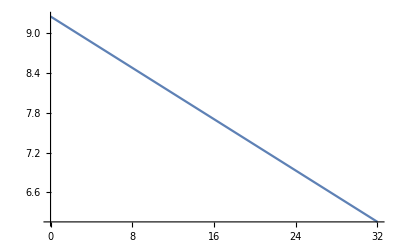

```mathematica
forFit1=data1⟦2;;,{2,8}⟧;
forFit1Cr=data1⟦2;;,-1⟧;
degOfFree=2;
fit1=Module[{x},LinearModelFit[forFit1,x^Range[0,degOfFree-1]//Evaluate,x]];
fit1@"ParameterTable"
Plot[fit1@x, {x, 0, 32}]
```

```mathematica
χ=√(Total[(print@fit1["FitResiduals"]/print@forFit1Cr)^2]/(Length[forFit1]-degOfFree));
χ^2
```

{0.015088,-0.010376,0.018466,-0.039528,-0.00782802,0.024178}

{0.003,0.002,0.003,0.003,0.003,0.003}

83.8665

```mathematica
fit1["FitResiduals"]
```

{0.015088,-0.010376,0.018466,-0.039528,-0.00782802,0.024178}

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

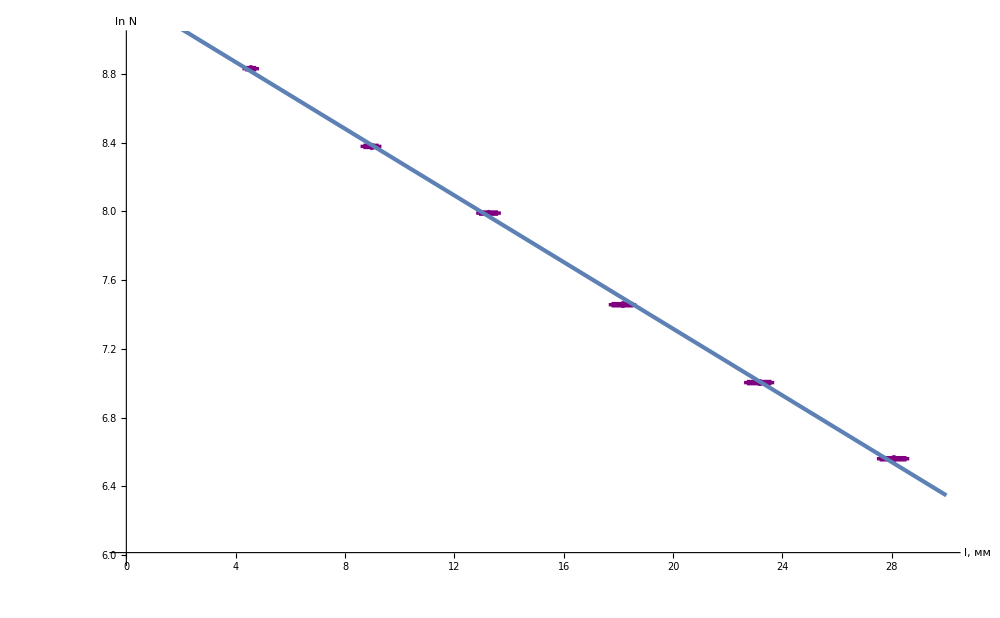

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data1⟦2;;,{2,8,3,9}⟧,
GridLines->{grids@1,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"l, мм","ln N"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,29.9},{6,8.99}}], 
Plot[fit1["Function"]@x,{x,0,30}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX1=MapAt[dropLastDot@*ToString,data1,{{2;;,All}}];
forTeX1//TeXForm
```

\left(
\begin{array}{ccccccccc}
 \unicode{2116} & \text{l} & \text{} & \text{N'} & \text{t} & \text{N} & \text{s N} & \text{ln N} & \text{s ln N} \\
 1 & 4.55 & 0.2 & 137190 & 20 & 6835 & 19 & 8.83 & 0.003 \\
 2 & 8.95 & 0.28 & 175029 & 40 & 4351 & 10 & 8.378 & 0.002 \\
 3 & 13.25 & 0.35 & 119005 & 40 & 2950 & 9 & 7.99 & 0.003 \\
 4 & 18.15 & 0.4 & 105458 & 60 & 1733 & 5 & 7.457 & 0.003 \\
 5 & 23.15 & 0.45 & 101334 & 90 & 1101 & 4 & 7.004 & 0.003 \\
 6 & 28.05 & 0.49 & 109744 & 150 & 707 & 2 & 6.561 & 0.003 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/51/tables/fe.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data2//TableForm
```

№ | l |  | N' | t | N | s N | ln N | s ln N
1. | 10.4 | 0.2 | 190381. | 30. | 6321. | 15. | 8.752 | 0.002
2. | 20.4 | 0.28 | 114002. | 30. | 3775. | 11. | 8.236 | 0.003
3. | 30.5 | 0.35 | 130668. | 60. | 2153. | 6. | 7.675 | 0.003
4. | 40.55 | 0.4 | 115211. | 90. | 1255. | 4. | 7.135 | 0.003
5. | 50.6 | 0.45 | 106440. | 140. | 735. | 2. | 6.6 | 0.003
6. | 60.8 | 0.49 | 114715. | 240. | 453. | 1. | 6.116 | 0.003

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[9.29634-0.0528208 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.29634 | 0.0226316 | 410.768 | 2.1074×10^-10
x | -0.0528208 | 0.000573124 | -92.1628 | 8.30973×10^-8

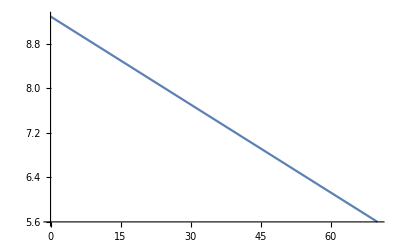

```mathematica
forFit2=data2⟦2;;,{2,8}⟧;
fit2=LinearModelFit[forFit2,{1,x},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 70}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

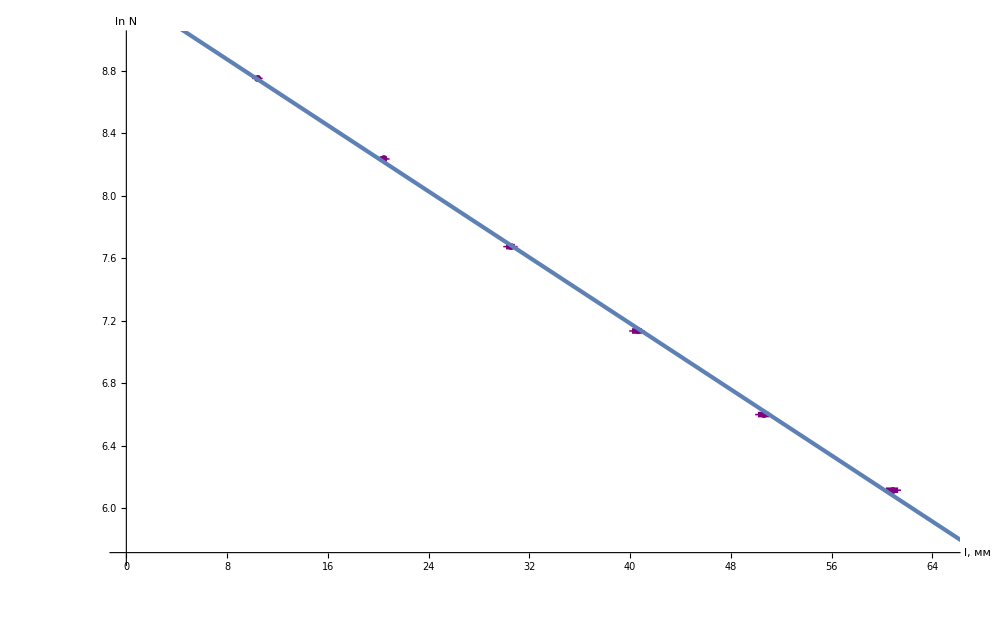

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data2⟦2;;,{2,8,3,9}⟧,
GridLines->{grids@1,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"l, мм","ln N"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,64.9},{5.7,8.99}}], 
Plot[fit2["Function"]@x,{x,0,100}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX2=MapAt[dropLastDot@*ToString,data2,{{2;;,All}}];
forTeX2//TeXForm
```

\left(
\begin{array}{ccccccccc}
 \unicode{2116} & \text{l} & \text{} & \text{N'} & \text{t} & \text{N} & \text{s N} & \text{ln N} & \text{s ln N} \\
 1 & 10.4 & 0.2 & 190381 & 30 & 6321 & 15 & 8.752 & 0.002 \\
 2 & 20.4 & 0.28 & 114002 & 30 & 3775 & 11 & 8.236 & 0.003 \\
 3 & 30.5 & 0.35 & 130668 & 60 & 2153 & 6 & 7.675 & 0.003 \\
 4 & 40.55 & 0.4 & 115211 & 90 & 1255 & 4 & 7.135 & 0.003 \\
 5 & 50.6 & 0.45 & 106440 & 140 & 735 & 2 & 6.6 & 0.003 \\
 6 & 60.8 & 0.49 & 114715 & 240 & 453 & 1 & 6.116 & 0.003 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data3=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/51/tables/al.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data3//TableForm
```

№ | l |  | N' | t | N | s N | ln N | s ln N
1. | 19.9 | 0.2 | 159422. | 20. | 7946. | 20. | 8.98 | 0.003
2. | 39.7 | 0.28 | 159510. | 30. | 5292. | 13. | 8.574 | 0.003
3. | 59.8 | 0.35 | 142914. | 40. | 3548. | 9. | 8.174 | 0.003
4. | 79.7 | 0.4 | 132888. | 60. | 2190. | 6. | 7.692 | 0.003
5. | 99.8 | 0.45 | 145262. | 90. | 1589. | 4. | 7.371 | 0.003

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[9.38483-0.0205191 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.38483 | 0.0416207 | 225.485 | 1.92349×10^-7
x | -0.0205191 | 0.000629458 | -32.598 | 0.0000634494

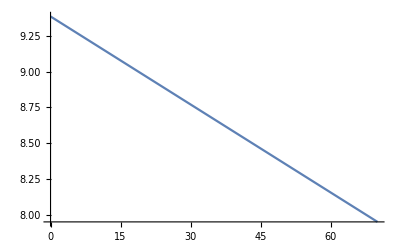

```mathematica
forFit3=data3⟦2;;,{2,8}⟧;
fit3=LinearModelFit[forFit3,{1,x},x]
fit3@"ParameterTable"
Plot[fit3["Function"]@x, {x, 0, 70}]
```

```mathematica
fit1["FitResiduals"]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

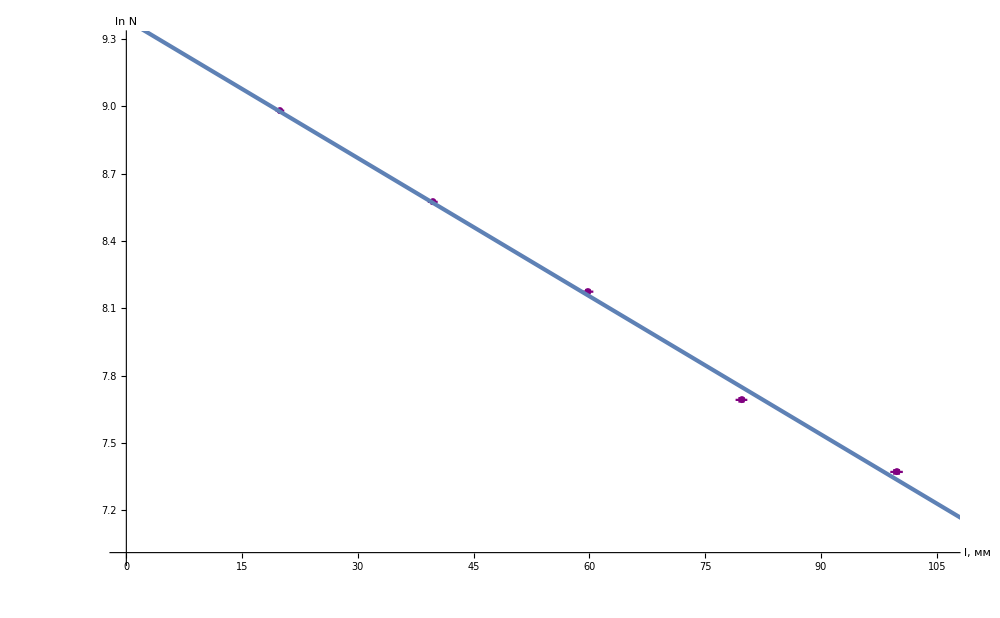

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data3⟦2;;,{2,8,3,9}⟧,
GridLines->{grids@2.5,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"l, мм","ln N"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,105.9},{7,9.29}}], 
Plot[fit3["Function"]@x,{x,0,150}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX3=MapAt[dropLastDot@*ToString,data3,{{2;;,All}}];
forTeX3//TeXForm
```

\left(
\begin{array}{ccccccccc}
 \unicode{2116} & \text{l} & \text{} & \text{N'} & \text{t} & \text{N} & \text{s N} & \text{ln N} & \text{s ln N} \\
 1 & 19.9 & 0.2 & 159422 & 20 & 7946 & 20 & 8.98 & 0.003 \\
 2 & 39.7 & 0.28 & 159510 & 30 & 5292 & 13 & 8.574 & 0.003 \\
 3 & 59.8 & 0.35 & 142914 & 40 & 3548 & 9 & 8.174 & 0.003 \\
 4 & 79.7 & 0.4 & 132888 & 60 & 2190 & 6 & 7.692 & 0.003 \\
 5 & 99.8 & 0.45 & 145262 & 90 & 1589 & 4 & 7.371 & 0.003 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data4=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/51/tables/d.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data4//TableForm
```

№ | l |  | N' | t | N | s N | ln N | s ln N
1. | 19.5 | 0.2 | 237645. | 20. | 11857. | 24. | 9.381 | 0.002
2. | 39.5 | 0.28 | 231631. | 20. | 11557. | 24. | 9.355 | 0.002
3. | 59.5 | 0.35 | 227327. | 20. | 11341. | 24. | 9.336 | 0.002
4. | 79.5 | 0.4 | 222510. | 20. | 11101. | 24. | 9.315 | 0.002
5. | 98.5 | 0.45 | 219907. | 20. | 10970. | 23. | 9.303 | 0.002
6. | 118.5 | 0.49 | 215922. | 20. | 10771. | 23. | 9.285 | 0.002

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[9.39488-0.000950058 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.39488 | 0.00365683 | 2569.13 | 1.37723×10^-13
x | -0.000950058 | 0.0000475104 | -19.9969 | 0.000036906

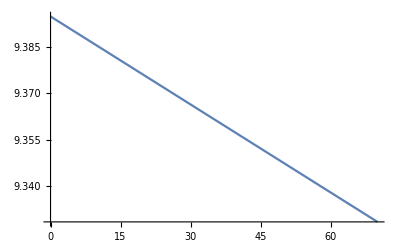

```mathematica
forFit4=data4⟦2;;,{2,8}⟧;
fit4=LinearModelFit[forFit4,{1,x},x]
fit4@"ParameterTable"
Plot[fit4["Function"]@x, {x, 0, 70}]
```

```mathematica
fit4["FitResiduals"]
```

{0.0046471,-0.00235173,-0.00235057,-0.0043494,0.00170172,0.00270288}

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

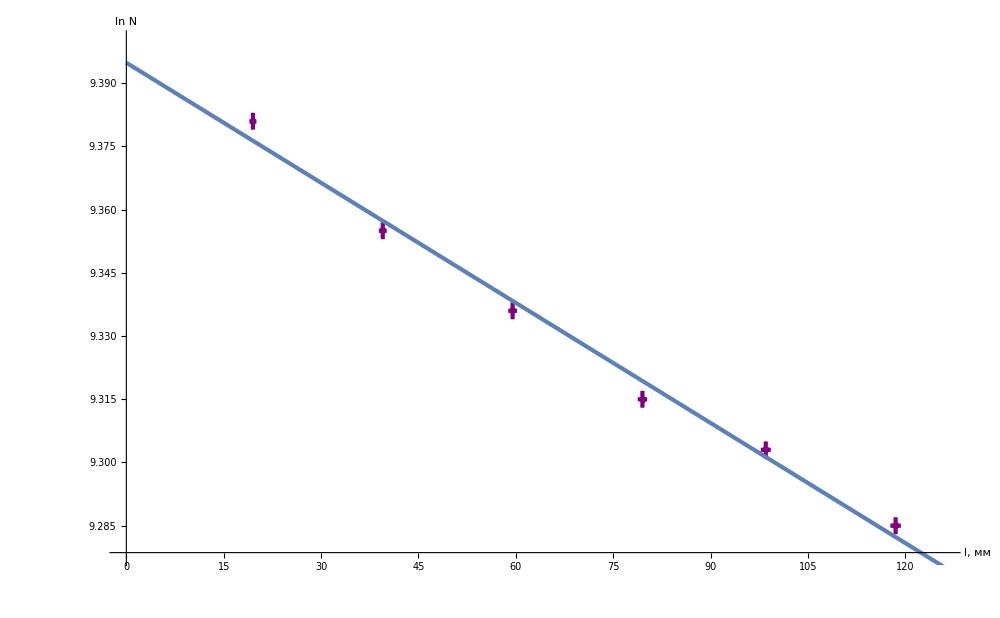

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data4⟦2;;,{2,8,3,9}⟧,
GridLines->{grids@2.5,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"l, мм","ln N"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,125.9},{9.278,9.39999}}], 
Plot[fit4["Function"]@x,{x,0,150}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX4=MapAt[dropLastDot@*ToString,data4,{{2;;,All}}];
forTeX4//TeXForm
```

\left(
\begin{array}{ccccccccc}
 \unicode{2116} & \text{l} & \text{} & \text{N'} & \text{t} & \text{N} & \text{s N} & \text{ln N} & \text{s ln N} \\
 1 & 19.5 & 0.2 & 237645 & 20 & 11857 & 24 & 9.381 & 0.002 \\
 2 & 39.5 & 0.28 & 231631 & 20 & 11557 & 24 & 9.355 & 0.002 \\
 3 & 59.5 & 0.35 & 227327 & 20 & 11341 & 24 & 9.336 & 0.002 \\
 4 & 79.5 & 0.4 & 222510 & 20 & 11101 & 24 & 9.315 & 0.002 \\
 5 & 98.5 & 0.45 & 219907 & 20 & 10970 & 23 & 9.303 & 0.002 \\
 6 & 118.5 & 0.49 & 215922 & 20 & 10771 & 23 & 9.285 & 0.002 \\
\end{array}
\right)